```mathematica
SetDirectory["C:\\Users\\Anton\\Dropbox\\Work\\2015-09 Slow cooling rates with Sarah Loewy\\Calculations\\Anim\\Frames"]
Directory[]
```

C:\Users\Anton\Dropbox\Work\2015-09 Slow cooling rates with Sarah Loewy\Calculations\Anim\Frames

C:\Users\Anton\Dropbox\Work\2015-09 Slow cooling rates with Sarah Loewy\Calculations\Anim\Frames

```mathematica
(*Setup*)
U1=DiagonalMatrix[{n/Sqrt[2],n,n}]; (*This is if it is fcc to bcc*)
U2=DiagonalMatrix[{n,n/Sqrt[2],n}];
U3=DiagonalMatrix[{n,n,n/Sqrt[2]}];
nvol=2^(1/6);
cof[m_]:=Transpose[Map[Reverse,Minors[Transpose[m],2],{0,1}] Table[(-1)^(i+j),{i,3},{j,3}]]/Det[U1]
inv[m_]:=Map[Reverse,Minors[Transpose[m],2],{0,1}] Table[(-1)^(i+j),{i,3},{j,3}]/Det[U1]
sq=Function[A,Transpose[A].A];
Frob[m_]:=Sqrt[Tr[sq[m]]];
norm=Function[a,Dot[a,a]^(1/2)];
normal=Function[a,a/norm[a]];
Mal1=Function[{A,f},Outer[Times,-2*(A.e-(1/Dot[cof[A].e,cof[A].e])*cof[A].e),e]]/.e->normal[f];
Mal1s=Function[{A,f},-2*(A.e-(1/Dot[cof[A].e,cof[A].e])*cof[A].e)]/.e->normal[f]; (*Shear*)
Mal1n=Function[{A,f},e]/.e->normal[f]; (*Normal*)

Mal2=Function[{A,f},Outer[Times,2*A.e,e-(1/Dot[A.e,A.e])*Transpose[A].A.e]]/.e->normal[f];
Mal2s=Function[{A,f},2*A.e]/.e->normal[f];
Mal2n=Function[{A,f},e-(1/Dot[A.e,A.e])*Transpose[A].A.e]/.e->normal[f];
```

```mathematica
(*Analyse the difference between the two different Type I solutions in simple laminates*)
L12p[v_]:=U1+v*Mal1[U1,{1,1,0}]
L12m[v_]:=U1+v*Mal1[U1,{1,-1,0}]
Manipulate[Plot[{1,SingularValueList[L12m[v]/.{n->k}]},{v,0,1}],{k,1.12,1.17}];
```

```mathematica
(*First solution - (557) - obtained from Det[sq[M]-id]==0*)
(*Here M[v_,k_]:=Simplify[U1+v*Mal1 @@{U1,{1/√2,1/√2,0}}+k*Mal1@@{U1+v*Mal1@@{U1,{1/√2,1/√2,0}},{0,1/√2,-1/√2}}]*)
f1:=Function[{n,m,mu},1/2+Sqrt[(-((n^2-3)*(m-n)^4*(m+n)^4*mu^4+(2*(2*n^4+m^2-5*n^2))*(m-n)^3*(m+n)^3*mu^3-(2*(m^4*n^4+m^2*n^6-4*m^4*n^2-5*m^2*n^4-3*n^6+2*m^4+3*m^2*n^2+7*n^4-m^2-n^2))*(m-n)^2*(m+n)^2*mu^2-(2*(m-n))*(m+n)*(m^2+n^2)*(2*m^2*n^6+2*m^4*n^2-6*m^2*n^4-2*n^6-m^4+2*m^2*n^2+5*n^4-2*n^2)*mu-(n-1)*(n+1)*(m^2+n^2)^2*(m^2+n^2-2)*(2*m^2*n^2-m^2-n^2))/((3*n^2-1)*(m-n)^2*(m+n)^2*mu^2+2*n^2*(m-n)*(m+n)*(m^2+n^2)*mu+(n-1)*(n+1)*(m^2+n^2)^2))]/((2*(mu-1))*(m+n)*(m-n))];
g1[mu_,n_]:=FullSimplify[f1[n,n/Sqrt[2],1-mu]];
g11[mu_,n_]:=g1[mu,n];
g12[mu_,n_]:=1-g1[mu,n];
```

```mathematica
(*Find admissible intervalls*)
lambda0[n_]:=N[g1[1,n]]
mu0l[n_]:=N[mu/.Solve[g1[mu,n]==1,mu]]
mu0r[n_]:=Select[N[mu/.Solve[g1[mu,n]==1/2,mu]][[2;;]],Im[#]==0&]
Points1[n_]:=Sort[Flatten[{mu0l[n],mu0r[n]}]]
Int1[n_]:=If[Length[Points1[n]]==3,IntervalUnion[Interval[Points1[n][[1;;2]]],Interval[{Points1[n][[3]],1}]],IntervalUnion[Interval[Points1[n][[1;;2]]],Interval[Points1[n][[3;;4]]],Interval[{Points1[n][[5]],1}]]]
Manipulate[Int1[n],{n,1.12,1.135}];
```

```mathematica
Manipulate[{mu0l[n],mu0r[n],Plot[{g11[mu,n],g12[mu,n]},{mu,0,1},PlotRange->{{0,1},{0,1}}]},{n,1.12,1.135}];
Manipulate[Plot[{g11[mu,n],g12[mu,n]},{mu,0,1},PlotRange->{{0,1},{0,1}}],{n,1.12,1.135}];
```

```mathematica
(*Second solution - (111) *)
f2:=Function[{n,m,mu},1/2+(1/2)*Sqrt[(-(3*m^4*mu^2*n^2-2*m^4*n^4-6*m^2*mu^2*n^4-2*m^2*n^6+3*mu^2*n^6-4*m^4*mu*n^2+6*m^2*mu*n^4-2*mu*n^6-m^4*mu^2+3*m^4*n^2+2*m^2*mu^2*n^2+4*m^2*n^4-mu^2*n^4+n^6+2*m^4*mu-2*m^2*mu*n^2-m^4-2*m^2*n^2-n^4)*(m^4*mu^2-2*m^2*mu^2*n^2+mu^2*n^4-2*m^4*mu+2*m^2*mu*n^2+m^4+2*m^2*n^2+n^4-2*m^2-2*n^2))]/((m^4*mu^2*n^2-2*m^2*mu^2*n^4+mu^2*n^6-3*m^4*mu^2+m^4*n^2+6*m^2*mu^2*n^2+2*m^2*n^4-3*mu^2*n^4+n^6+2*m^4*mu-2*mu*n^4-m^4-2*m^2*n^2-n^4)^(1/2)*(mu-1)*(m+n)*(m-n))];
g2[mu_,n_]:=FullSimplify[f2[n,n/Sqrt[2],1-mu]];
g21[mu_,n_]:=g2[mu,n];
g22[mu_,n_]:=1-g2[mu,n];
```

```mathematica
Manipulate[Plot[{g21[mu,n],g22[mu,n]},{mu,0,1},PlotRange->{{0,1},{0,1}}],{n,1.12,1.135}];
```

```mathematica
(*Find admissible Intervals*)
lambda02[n_]:=N[g2[1,n]]
mu0inv2[n_]:=N[mu/.Solve[g2[mu,n]==1/2,mu]][[3]]
Int2[n_]:=IntervalUnion[Interval[{1-lambda02[n],lambda02[n]}],Interval[{mu0inv2[n],1}]];
Manipulate[Int2[n],{n,1.12,1.135}];
```

```mathematica
(*Let's do some consistency checks*)
F1[v_,k_]=Simplify[U1+v*Mal1 @@{U1,{1/√2,1/√2,0}}+(g11[v,n])*Mal1@@{U1+v*Mal1@@{U1,{1/√2,1/√2,0}},{0,1/√2,-1/√2}}]/.{n->k};
F2[v_,k_]=Simplify[U1+v*Mal1 @@{U1,{1/√2,1/√2,0}}+(g21[v,n])*Mal2@@{U1+v*Mal1@@{U1,{1/√2,1/√2,0}},{0,1/√2,-1/√2}}]/.{n->k};
```

```mathematica
(*Test Middle Singular value*)
(*Table[Plot[SingularValueList[F1[mu,n]],mu∈Int1[n]],{n,1.12,1.14,.01}]
Table[Plot[SingularValueList[F2[mu,n]],mu∈Int2[n]],{n,1.12,1.14,.01}]*)
```

```mathematica
(*Now Plot the normals for these*)
LAM1[v_,n_]=Simplify[sq[F1[v,n]]];
LAM2[v_,n_]=Simplify[sq[F2[v,n]]];
```

```mathematica
(*These are all the functions needed for plotting Vectors*)
b=(-a11-a22-a33);
c=(-a12^2-a13^2+a11 a22-a23^2+a11 a33+a22 a33);
d=a13^2 a22-2 a12 a13 a23+a11 a23^2+a12^2 a33-a11 a22 a33;
com=Function[A,{A[[1,1]],A[[2,2]],A[[3,3]],A[[1,2]],A[[1,3]],A[[2,3]]}];
e1=Function[{a11,a12,a13,a21,a22,a23,a31,a32,a33},1/2*(-b-1-Sqrt[b^2-4*c-2*b-3])];
e1s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[e1[a11,a12,a13,a12,a22,a23,a13,a23,a33]];

e3=Function[{a11,a12,a13,a21,a22,a23,a31,a32,a33},1/2*(-b-1+Sqrt[b^2-4*c-2*b-3])];
e3s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[e3[a11,a12,a13,a12,a22,a23,a13,a23,a33]];

e2s[a11_,a22_,a33_,a12_,a13_,a23_]=1;
evector1[a11_,a12_,a13_,a21_,a22_,a23_,a31_,a32_,a33_]=FullSimplify[
{-(a33-e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])*(-a22 a31+a21 a32+a31 e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])
+(a32 (-a23 a31+a21 a33-a21 e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])),-((-a23 a31+a21 a33-a21 e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])*a31),a31 (-a22 a31+a21 a32+a31 e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])}];
ev1s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[evector1[a11,a12,a13,a12,a22,a23,a13,a23,a33]];
nev1s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[normal[ev1s[a11,a22,a33,a12,a13,a23]]];

evector3[a11_,a12_,a13_,a21_,a22_,a23_,a31_,a32_,a33_]=
FullSimplify[{-(a33-e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])*(-a22 a31+a21 a32+a31 e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])
+(a32 (-a23 a31+a21 a33-a21 e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])),-((-a23 a31+a21 a33-a21 e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])*a31),a31 (-a22 a31+a21 a32+a31 e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])}];
ev3s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[evector3[a11,a12,a13,a12,a22,a23,a13,a23,a33]];
nev3s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[normal[ev3s[a11,a22,a33,a12,a13,a23]]];
```

```mathematica
(*Simplify the Components*)
LAM1com[v_,n_]=Simplify[com[LAM1[v,n]]];
LAM2com[v_,n_]=Simplify[com[LAM2[v,n]]];
```

```mathematica
bainnormalm1[v_,n_]:=-Sqrt[1-e1s @@LAM1com[v,n]]*nev1s@@LAM1com[v,n]-Sqrt[-1+e3s@@LAM1com[v,n]]*nev3s@@LAM1com[v,n];
bainnormalp1[v_,n_]:=-Sqrt[1-e1s @@LAM1com[v,n]]*nev1s@@LAM1com[v,n]+Sqrt[-1+e3s@@LAM1com[v,n]]*nev3s@@LAM1com[v,n];
bainnormalm2[v_,n_]:=-Sqrt[1-e1s @@LAM2com[v,n]]*nev1s@@LAM2com[v,n]-Sqrt[-1+e3s@@LAM2com[v,n]]*nev3s@@LAM2com[v,n];
bainnormalp2[v_,n_]:=-Sqrt[1-e1s @@LAM2com[v,n]]*nev1s@@LAM2com[v,n]+Sqrt[-1+e3s@@LAM2com[v,n]]*nev3s@@LAM2com[v,n];
```

```mathematica
P1=IdentityMatrix[3];
P2={{0,-1,0},{-1,0,0},{0,0,-1}};
P4={{0,0,-1},{0,-1,0},{-1,0,0}};
P3={{0,1,0},{0,0,1},{1,0,0}};
P5={{0,0,1},{1,0,0},{0,1,0}};
P6={{-1,0,0},{0,0,-1},{0,-1,0}};
P8={{1,0,0},{0,-1,0},{0,0,-1}};
P7={{0,1,0},{-1,0,0},{0,0,1}};
P9={{0,0,1},{0,1,0},{-1,0,0}};
P10={{0,-1,0},{0,0,-1},{1,0,0}};
P12={{0,0,-1},{1,0,0},{0,-1,0}};
P11={{-1,0,0},{0,0,1},{0,1,0}};
P13={{0,-1,0},{1,0,0},{0,0,1}};
P14={{-1,0,0},{0,1,0},{0,0,-1}};
P18={{0,0,-1},{-1,0,0},{0,1,0}};
P17={{1,0,0},{0,0,1},{0,-1,0}};
P15={{0,0,1},{0,-1,0},{1,0,0}};
P16={{0,1,0},{0,0,-1},{-1,0,0}};
P23={{1,0,0},{0,0,-1},{0,1,0}};
P24={{0,0,1},{-1,0,0},{0,-1,0}};
P22={{0,-1,0},{0,0,1},{-1,0,0}};
P21={{0,0,-1},{0,1,0},{1,0,0}};
P19={{0,1,0},{1,0,0},{0,0,-1}};
P20={{-1,0,0},{0,-1,0},{0,0,1}};
PP={P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20,P21,P22,P23,P24};
PP48=Flatten[{PP,-PP},1];
```

```mathematica
B1PPlist={1,6,8,11,14,17,20,23,25,30,32,35,38,41,44,47}; (*maps B1 to itself*)
B2PPlist={2,3,7,10,13,16,19,22,26,27,31,34,37,40,43,46} ;(*maps B1 to B2, i.e. PP[[i]]^T B_1 PP[[i]]=B2*)
B3PPlist={4,5,9,12,15,18,21,24,28,29,33,36,39,42,45,48};  (*maps B1 to B3*)
```

```mathematica
(*Nice output plot with spheres*)
sp1=SphericalPlot3D[1,{θ,0,Pi},{ϕ,0,2Pi},PlotStyle->{White,Opacity[1]},Lighting->"Neutral",Boxed->False,Axes->False];
BlueSphere[{x_,y_,z_}]:=Graphics3D[{Style[Sphere[{x,y,z},0.03],Blue, Opacity[.5]]}];
YellowSphere[{x_,y_,z_}]:=Graphics3D[{Style[Sphere[{x,y,z},0.03],Yellow, Opacity[.5]]}];
CyanSphere[{x_,y_,z_}]:=Graphics3D[{Style[Sphere[{x,y,z},0.03],Cyan, Opacity[.5]]}];
GreenSphere[{x_,y_,z_}]:=Graphics3D[{Style[Sphere[{x,y,z},0.03],Green, Opacity[.5]]}];
```

```mathematica
ff7=Function[i,PP48[[i]].N[Normalize[{5,5,7}]]]/@Range[24];
tt3=Flatten[{Function[i,PP[[i]].N[Normalize[{2,2,3}]]]/@Range[24],Function[i,-PP[[i]].N[Normalize[{2,2,3}]]]/@Range[24]},1];
oo1=Function[i,PP[[i]].N[Normalize[{1,1,1}]]]/@Range[24];
h=Function[{n,m},(Sqrt[m^2+n^2-2*n^2*m^2]-Sqrt[2-n^2-m^2])];
k=Function[{n,m},(Sqrt[m^2+n^2-2*n^2*m^2]+Sqrt[2-n^2-m^2])];
l=Function[{n,m},(2*Sqrt[n^2-1])];
normalsimple[n_,m_]:=Normalize[{h[n,m],k[n,m],l[n,m]}];
tt15[n_]:=PP48[[#]].normalsimple[n,n/Sqrt[2]]&/@Range[48];
```

```mathematica
plotff7=Map[BlueSphere,ff7];
plottt3=Map[CyanSphere,tt3];
plotoo1=Map[GreenSphere,oo1];
plottt15[n_]:=Map[YellowSphere,tt15[n]];
```

```mathematica
(*Define the Strain energy function for cut-off of noise*)
(*the 1-Strain Energy*)
dist1=Function[A,Norm[Sqrt[Eigenvalues[A]]-{1,1,1}]^2];
Strain1[v_,n_]:=dist1[LAM1[v,n]];
Strain2[v_,n_]:=dist1[LAM2[v,n]];
```

```mathematica
ColorF[c_,x_]:=Hue[c,1,.7,.6*(1-HeavisideTheta[x-.025])]
```

```mathematica
(*Sample the Intervall*)
LinePlot1m[n_,Int_,i_,c_]:=ParametricPlot3D[Transpose[PP48[[i]]].normal[bainnormalm1[k,n]],k∈Int,ColorFunction->Function[{x,y,z,t},ColorF[c,Strain1[t,n]]],ColorFunctionScaling->False,MaxRecursion->4,PlotPoints->800]
LinePlot1p[n_,Int_,i_,c_]:=ParametricPlot3D[Transpose[PP48[[i]]].normal[bainnormalp1[k,n]],k∈Int,ColorFunction->Function[{x,y,z,t},ColorF[c,Strain1[t,n]]],ColorFunctionScaling->False,MaxRecursion->4,PlotPoints->800]
LinePlot2m[n_,Int_,i_,c_]:=ParametricPlot3D[Transpose[PP48[[i]]].normal[bainnormalm2[k,n]],k∈Int,ColorFunction->Function[{x,y,z,t},ColorF[c,Strain2[t,n]]],ColorFunctionScaling->False,MaxRecursion->4,PlotPoints->800]
LinePlot2p[n_,Int_,i_,c_]:=ParametricPlot3D[Transpose[PP48[[i]]].normal[bainnormalp2[k,n]],k∈Int,ColorFunction->Function[{x,y,z,t},ColorF[c,Strain2[t,n]]],ColorFunctionScaling->False,MaxRecursion->4,PlotPoints->800]
```

```mathematica
PlotBain1[n_]:=Show[sp1,plottt15[n],plotff7,
LinePlot1m[n,Int1[n],#,.4]&/@B1PPlist,LinePlot1m[n,Int1[n],#,.6]&/@B2PPlist,LinePlot1m[n,Int1[n],#,1]&/@B3PPlist,
LinePlot1p[n,Int1[n],#,.4]&/@B1PPlist,LinePlot1p[n,Int1[n],#,.6]&/@B2PPlist,LinePlot1p[n,Int1[n],#,1]&/@B3PPlist,
PlotLabel-> Style[{StringJoin["η=",ToString[NumberForm[n,{5,5}]]],StringJoin["Δ=",ToString[NumberForm[(n^3/Sqrt[2]-1)*100,{5,5}]],"%"]},18],
ViewPoint->{1.2,1.2,1.4}];
Do[Export["Bain1c_"<>ToString[NumberForm[n,{5,5}]]<>".PNG",PlotBain1[n],"PNG",ImageResolution->400],{n,1.12,1.1364,.0001}];
```

```mathematica
PlotBain2[n_]:=Show[sp1,plottt15[n],plotoo1,
LinePlot2m[n,Int2[n],#,.4]&/@B1PPlist,LinePlot2m[n,Int2[n],#,.6]&/@B2PPlist,LinePlot2m[n,Int2[n],#,1]&/@B3PPlist,
LinePlot2p[n,Int2[n],#,.4]&/@B1PPlist,LinePlot2p[n,Int2[n],#,.6]&/@B2PPlist,LinePlot2p[n,Int2[n],#,1]&/@B3PPlist,
PlotLabel-> Style[{StringJoin["η=",ToString[NumberForm[n,{5,5}]]],StringJoin["Δ=",ToString[NumberForm[(n^3/Sqrt[2]-1)*100,{5,5}]],"%"]},18],
ViewPoint->{1.2,1.2,1.4}]
Do[Export["Bain2c_"<>ToString[NumberForm[n,{5,5}]]<>".PNG",PlotBain2[n],"PNG",ImageResolution->400],{n,1.12,1.1364,.0001}];
```

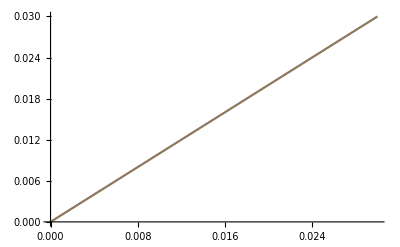

```mathematica
Plot[x,{x,0,.03},ColorFunction->Function[{x,y},Hue[2.3*(.28-10*x),1,1,1-HeavisideTheta[x-.025]]],ColorFunctionScaling->False]
```

```mathematica
Graphics3D[{Opacity[.7],{Hue[#],Cuboid[#,#+.1]}&/@Tuples[Range[0,1,.2],3]},Axes->True,AxesLabel->{"Hue","Saturation","Brightness"},Lighting->"Neutral"]
```

-Graphics3D-

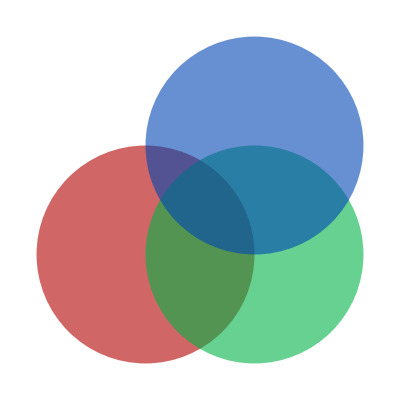

```mathematica
Show[Graphics[{Hue[1,1,.7,.6],Disk[]}],
Graphics[{Hue[.4,1,.7,.6],Disk[{1,0}]}],
Graphics[{Hue[.6,1,.7,.6],Disk[{1,1}]}]]
```

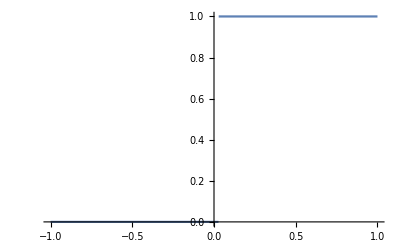

```mathematica
Plot[HeavisideTheta[x-.028],{x,-1,1}]
```